## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.5; qscal=0.7; Q=0.997;
```

```mathematica
winit=(0.45-0.00005*I)
```

0.45-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.516918+1.09482×10^-10 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=45; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.647762

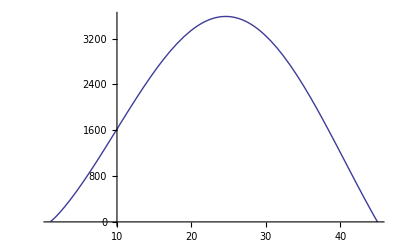

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.45+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.4+0.000005*I);
ie=0;While[ie<176,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=45-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,175}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,175}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{45.,1.0948×10^-10},{44.8,1.12702×10^-10},{44.6,1.15976×10^-10},{44.4,1.19383×10^-10},{44.2,1.22901×10^-10},{44.,1.26532×10^-10},{43.8,1.30287×10^-10},{43.6,1.34834×10^-10},{43.4,1.38161×10^-10},{43.2,1.45292×10^-10},{43.,1.46571×10^-10},{42.8,1.50986×10^-10},{42.6,1.5555×10^-10},{42.4,1.60249×10^-10},{42.2,1.65138×10^-10},{42.,1.70181×10^-10},{41.8,1.75387×10^-10},{41.6,1.80795×10^-10},{41.4,1.86341×10^-10},{41.2,1.92101×10^-10},{41.,1.98058×10^-10},{40.8,2.04202×10^-10},{40.6,2.10451×10^-10},{40.4,2.17195×10^-10},{40.2,2.24959×10^-10},{40.,2.31083×10^-10},{39.8,2.38423×10^-10},{39.6,2.45502×10^-10},{39.4,2.53614×10^-10},{39.2,2.57579×10^-10},{39.,2.7031×10^-10},{38.8,2.79006×10^-10},{38.6,2.88043×10^-10},{38.4,2.96294×10^-10},{38.2,3.07048×10^-10},{38.,3.17036×10^-10},{37.8,3.27417×10^-10},{37.6,3.38174×10^-10},{37.4,3.49315×10^-10},{37.2,3.60875×10^-10},{37.,3.72867×10^-10},{36.8,3.85292×10^-10},{36.6,3.98176×10^-10},{36.4,4.11539×10^-10},{36.2,4.25402×10^-10},{36.,4.39666×10^-10},{35.8,4.56226×10^-10},{35.6,4.70179×10^-10},{35.4,4.86247×10^-10},{35.2,5.02921×10^-10},{35.,5.20148×10^-10},{34.8,5.38177×10^-10},{34.6,5.56824×10^-10},{34.4,5.76242×10^-10},{34.2,5.96368×10^-10},{34.,6.17274×10^-10},{33.8,6.41117×10^-10},{33.6,6.61561×10^-10},{33.4,6.85012×10^-10},{33.2,6.99717×10^-10},{33.,7.34722×10^-10},{32.8,7.6106×10^-10},{32.6,7.88446×10^-10},{32.4,8.16924×10^-10},{32.2,8.46527×10^-10},{32.,8.77346×10^-10},{31.8,9.10191×10^-10},{31.6,9.44582×10^-10},{31.4,9.77447×10^-10},{31.2,1.01295×10^-9},{31.,1.05115×10^-9},{30.8,1.09163×10^-9},{30.6,1.13104×10^-9},{30.4,1.17348×10^-9},{30.2,1.21767×10^-9},{30.,1.26371×10^-9},{29.8,1.31167×10^-9},{29.6,1.36164×10^-9},{29.4,1.41371×10^-9},{29.2,1.46798×10^-9},{29.,1.52455×10^-9},{28.8,1.58262×10^-9},{28.6,1.64503×10^-9},{28.4,1.70916×10^-9},{28.2,1.77093×10^-9},{28.,1.8458×10^-9},{27.8,1.91857×10^-9},{27.6,1.99453×10^-9},{27.4,2.07378×10^-9},{27.2,2.1565×10^-9},{27.,2.24439×10^-9},{26.8,2.33295×10^-9},{26.6,2.42706×10^-9},{26.4,2.52533×10^-9},{26.2,2.62795×10^-9},{26.,2.73514×10^-9},{25.8,2.84714×10^-9},{25.6,2.9641×10^-9},{25.4,3.08635×10^-9},{25.2,3.21775×10^-9},{25.,3.34757×10^-9},{24.8,3.48714×10^-9},{24.6,3.63302×10^-9},{24.4,3.78551×10^-9},{24.2,3.94497×10^-9},{24.,4.11171×10^-9},{23.8,4.28607×10^-9},{23.6,4.46064×10^-9},{23.4,4.65581×10^-9},{23.2,4.85868×10^-9},{23.,5.06737×10^-9},{22.8,5.28572×10^-9},{22.6,5.51418×10^-9},{22.4,5.75315×10^-9},{22.2,6.00324×10^-9},{22.,6.265×10^-9},{21.8,6.53868×10^-9},{21.6,6.82516×10^-9},{21.4,7.12493×10^-9},{21.2,7.43859×10^-9},{21.,7.76678×10^-9},{20.8,8.11015×10^-9},{20.6,8.46941×10^-9},{20.4,8.84523×10^-9},{20.2,9.23874×10^-9},{20.,9.64954×10^-9},{19.8,1.00795×10^-8},{19.6,1.05292×10^-8},{19.4,1.09992×10^-8},{19.2,1.14907×10^-8},{19.,1.20044×10^-8},{18.8,1.25405×10^-8},{18.6,1.31006×10^-8},{18.4,1.36853×10^-8},{18.2,1.42957×10^-8},{18.,1.49325×10^-8},{17.8,1.5597×10^-8},{17.6,1.62885×10^-8},{17.4,1.70092×10^-8},{17.2,1.77594×10^-8},{17.,1.85396×10^-8},{16.8,1.93502×10^-8},{16.6,2.01923×10^-8},{16.4,2.10652×10^-8},{16.2,2.19701×10^-8},{16.,2.29057×10^-8},{15.8,2.38725×10^-8},{15.6,2.48703×10^-8},{15.4,2.58963×10^-8},{15.2,2.69532×10^-8},{15.,2.80306×10^-8},{14.8,2.91341×10^-8},{14.6,3.02581×10^-8},{14.4,3.13971×10^-8},{14.2,3.25451×10^-8},{14.,3.36969×10^-8},{13.8,3.48432×10^-8},{13.6,3.59724×10^-8},{13.4,3.70706×10^-8},{13.2,3.81202×10^-8},{13.,3.90911×10^-8},{12.8,3.99737×10^-8},{12.6,4.07096×10^-8},{12.4,4.12537×10^-8},{12.2,4.15302×10^-8},{12.,4.14711×10^-8},{11.8,4.09238×10^-8},{11.6,3.97178×10^-8},{11.4,3.76217×10^-8},{11.2,3.42698×10^-8},{11.,2.9164×10^-8},{10.8,2.15739×10^-8},{10.6,1.04284×10^-8},{10.4,-5.8719×10^-9},{10.2,-2.96759×10^-8},{10.,-6.45921×10^-8}}

```mathematica
(*The imaginary part vs the radius*)
```

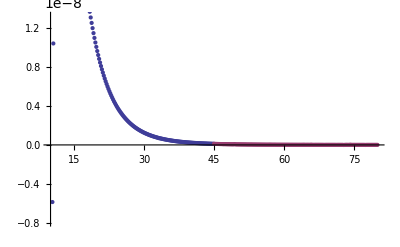

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

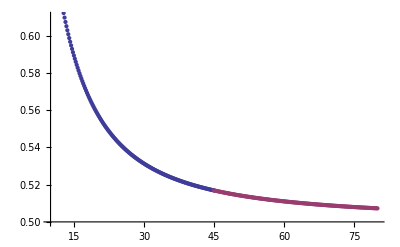

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.997/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.997/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.997/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/plots/ratio1.4/Q=0.997/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```